```mathematica
2-2
```

0

```mathematica
Subscript[R, effective][i_,j_]:=Γ⟦i⟧⟦i⟧+Γ⟦j⟧⟦j⟧-2Γ⟦i⟧⟦j⟧
```

# Internodal Resistances on Complete Graphs

Nicholas Wheeler
15 November 2011

### Introduction

I undertake this little project in connection with my belated discovery that the Klein-Randić method pertains only to connected graphs. Here I look, by way of preliminary exploration, to complete (∴ maximally connected) graphs of increasingly many nodes:

#### 2-node complete

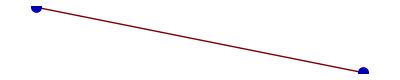

(0. | 1.
1. | 0.)

```mathematica
𝔾=({{0, 1}, {0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,2}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,2},{j,1,2}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02]]
𝕎//MatrixForm
```

#### 3-node complete

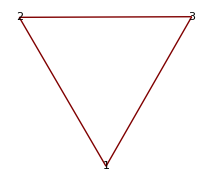

(0. | 0.666667 | 0.666667
0.666667 | 0. | 0.666667
0.666667 | 0.666667 | 0.)

```mathematica
𝔾=({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,3}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,3},{j,1,3}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02], VertexLabeling->True]
𝕎//MatrixForm
```

```mathematica
2/3//N
```

0.666667

#### 4-node complete

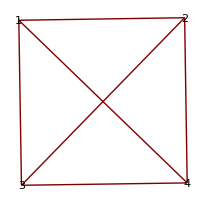

(0. | 0.5 | 0.5 | 0.5
0.5 | 0. | 0.5 | 0.5
0.5 | 0.5 | 0. | 0.5
0.5 | 0.5 | 0.5 | 0.)

```mathematica
𝔾=({{0, 1, 1, 1}, {0, 0, 1, 1}, {0, 0, 0, 1}, {0, 0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,4}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,4},{j,1,4}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02], VertexLabeling->True]
𝕎//MatrixForm
```

```mathematica
2/4//N
```

0.5

#### 5-node complete

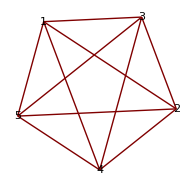

(0. | 0.4 | 0.4 | 0.4 | 0.4
0.4 | 0. | 0.4 | 0.4 | 0.4
0.4 | 0.4 | 0. | 0.4 | 0.4
0.4 | 0.4 | 0.4 | 0. | 0.4
0.4 | 0.4 | 0.4 | 0.4 | 0.)

```mathematica
𝔾=({{0, 1, 1, 1, 1}, {0, 0, 1, 1, 1}, {0, 0, 0, 1, 1}, {0, 0, 0, 0, 1}, {0, 0, 0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,5}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,5},{j,1,5}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02], VertexLabeling->True]
𝕎//MatrixForm
```

```mathematica
2/5//N
```

0.4

#### 6-node complete

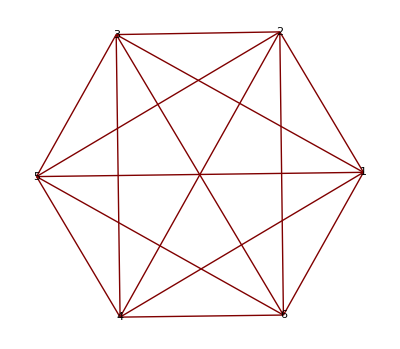

(0. | 0.333333 | 0.333333 | 0.333333 | 0.333333 | 0.333333
0.333333 | 0. | 0.333333 | 0.333333 | 0.333333 | 0.333333
0.333333 | 0.333333 | 0. | 0.333333 | 0.333333 | 0.333333
0.333333 | 0.333333 | 0.333333 | 0. | 0.333333 | 0.333333
0.333333 | 0.333333 | 0.333333 | 0.333333 | 0. | 0.333333
0.333333 | 0.333333 | 0.333333 | 0.333333 | 0.333333 | 0.)

```mathematica
𝔾=({{0, 1, 1, 1, 1, 1}, {0, 0, 1, 1, 1, 1}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,6}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,6},{j,1,6}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02], VertexLabeling->True]
𝕎//MatrixForm
```

```mathematica
2/6//N
```

0.333333

#### 7-node complete

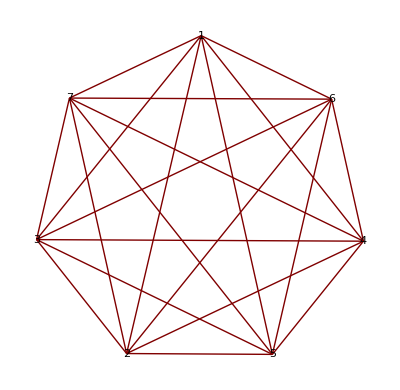

(0. | 0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.285714
0.285714 | 0. | 0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.285714
0.285714 | 0.285714 | 0. | 0.285714 | 0.285714 | 0.285714 | 0.285714
0.285714 | 0.285714 | 0.285714 | 0. | 0.285714 | 0.285714 | 0.285714
0.285714 | 0.285714 | 0.285714 | 0.285714 | 0. | 0.285714 | 0.285714
0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.285714 | 0. | 0.285714
0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.285714 | 0.)

```mathematica
𝔾=({{0, 1, 1, 1, 1, 1, 1}, {0, 0, 1, 1, 1, 1, 1}, {0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,7}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,7},{j,1,7}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02], VertexLabeling->True]
𝕎//MatrixForm
```

```mathematica
2/7//N
```

0.285714

#### 15-node complete

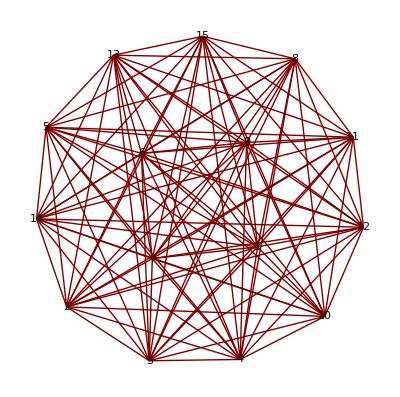

(0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333 | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0. | 0.133333
0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.133333 | 0.)

```mathematica
𝔾=({{0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,15}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];
𝕎=Table[Subscript[R, effective][i,j],{i,1,15},{j,1,15}];
GraphPlot[𝔾,PlotStyle->PointSize[0.02], VertexLabeling->True]
𝕎//MatrixForm
```

```mathematica
2/15//N
```

0.133333

### Conclusion, and a conjecture

It appears to be the case that on a circuit represented by a complete graph (all resistances set to unity) all internodal resistances are the same, and are given by

Internodal Resistance = 2/(Number of nodes)

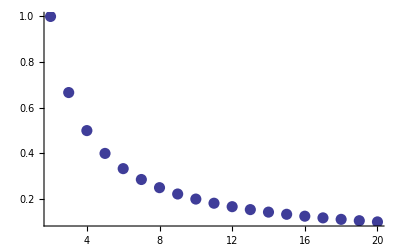

```mathematica
ListPlot[Table[{n,2/n},{n,2,20}], PlotStyle->PointSize[0.02]]
```

### Elementary arguments

The conjectured value of the resistance between any pair of nodes in this simplest of cases

-Graphics-

is 2/3. Here two parallel paths, with resistances 1 and 2, link any nodal pair, so we expect the effective resistance to be

```mathematica
(1/1+1/2)^-1
```

2/3

In this next-simplest case

-Graphics-

some nodes appear to be adjacent, others next-to-adjacent, but that is an artifact of the diagram (or better: of the way we tend to look at the diagram, our eye following the perimeter). In fact, the nodal interrelationships are symmetric, identical: every node is adjacent to every other. So the claim

```mathematica
𝕎=({{0, 1/2, 1/2, 1/2}, {1/2, 0, 1/2, 1/2}, {1/2, 1/2, 0, 1/2}, {1/2, 1/2, 1/2, 0}})
```

that all internodal resistances are the same is not at all mysterious. But by what elementary argument can one obtain the 1/2s? And in the next simplest case

-Graphics-

by what elementary argument can one establish that (as shown above) all internodal resistances are 2/5?

### A simple heuristic

Look to the following figure:

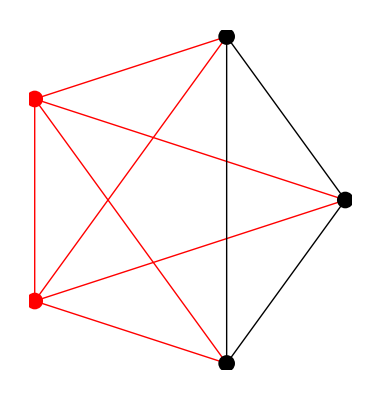

```mathematica
Table[Subscript[p, k]={Cos[(2π)/5(k-1)],Sin[(2π)/5(k-1)]},{k,1,5}];
nodes={
{PointSize[0.03],Point[Subscript[p, 1]]},
{PointSize[0.03],Point[Subscript[p, 2]]},
{Red,PointSize[0.03],Point[Subscript[p, 3]]},
{Red,PointSize[0.03],Point[Subscript[p, 4]]},
{PointSize[0.03],Point[Subscript[p, 5]]}};
edges={
{Red,Thick,Line[{Subscript[p, 3],Subscript[p, 4]}]},
{Red,Thick,Line[{Subscript[p, 3],Subscript[p, 2]}]},
{Red,Thick,Line[{Subscript[p, 4],Subscript[p, 2]}]},
{Red,Thick,Line[{Subscript[p, 3],Subscript[p, 1]}]},
{Red,Thick,Line[{Subscript[p, 4],Subscript[p, 1]}]},
{Red,Thick,Line[{Subscript[p, 3],Subscript[p, 5]}]},
{Red,Thick,Line[{Subscript[p, 4],Subscript[p, 5]}]},
Line[{Subscript[p, 2],Subscript[p, 5]}],
Line[{Subscript[p, 2],Subscript[p, 1]}],
Line[{Subscript[p, 5],Subscript[p, 1]}]};
Graphics[Join[ edges,nodes]]
```

Ask for the effective resistance between the red nodes. We see (neglecting—on what grounds?—the three black legs) four parallel branches, and immediately have

```mathematica
(1/1+1/2+1/2+1/2)^-1
```

2/5

The same argument, applied to a complete n-node graph, supplies

```mathematica
(1/1+(n-2)1/2)^-1//Simplify
```

2/n

—as was previously conjectured. 

So the question becomes: How to justify the heuristic?

### Detailed solution by application of the variational principle

The question posed above is made perplexing by our intuitive expectation—incorrect, as will soon emerge—that when the red nodes are connected to a power source current will in fact flow in the black edges.

Borrowing commands from Slide 29 in the notes from my "Experimental Mathematical Physics" seminar, I use the variational method to evaluate (on the assumption that the through current J = 1) the nodal potentials and effective resistance of the 5-node graph:

```mathematica
𝔾=({{0, 1, 1, 1, 1}, {0, 0, 1, 1, 1}, {0, 0, 0, 1, 1}, {0, 0, 0, 0, 1}, {0, 0, 0, 0, 0}});
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,5}]];
𝕃=𝔻-𝔸;
Diss=Expand[Transpose[({{Subscript[V, 1]}, {Subscript[V, 2]}, {Subscript[V, 3]}, {Subscript[V, 4]}, {Subscript[V, 5]}})].𝕃.({{Subscript[V, 1]}, {Subscript[V, 2]}, {Subscript[V, 3]}, {Subscript[V, 4]}, {Subscript[V, 5]}})]⟦1⟧;
Subscript[C, 12]=Table[Sum[𝕃⟦j⟧⟦k⟧Subscript[V, k],{k,1,5}]==KroneckerDelta[j,1]-KroneckerDelta[j,2],{j,1,5}];

Minimize[Flatten[{Diss,Subscript[C, 12]}],{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5]}]
```

{2/5,{V_1→1/5,V_2→-1/5,V_3→0,V_4→0,V_5→0}}

Adjusting the nodal potentials so that the exit node is grounded

```mathematica
Subscript[V, bluenode]=0
Subscript[V, rednode]=2/5
Subscript[V, blacknodes]=1/5
```

we arrive at the situation shown below:

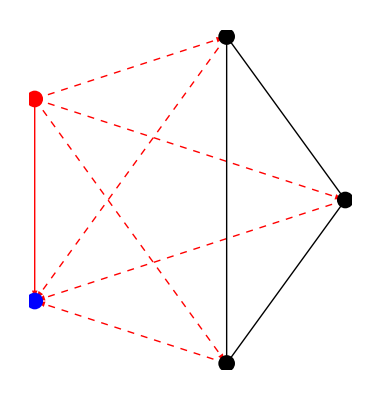

```mathematica
nodes2={
{PointSize[0.03],Point[Subscript[p, 1]]},
{PointSize[0.03],Point[Subscript[p, 2]]},
{Red,PointSize[0.03],Point[Subscript[p, 3]]},
{Blue,PointSize[0.03],Point[Subscript[p, 4]]},
{PointSize[0.03],Point[Subscript[p, 5]]}};
currents={
{Red,Thick,Arrow[{Subscript[p, 3],Subscript[p, 4]},{0,0.02}]},
{Red,Thick,Dashed,Arrow[{Subscript[p, 3],Subscript[p, 2]},{0,0.02}]},
{Red,Thick,Dashed,Arrow[{Subscript[p, 2],Subscript[p, 4]},{0,0.02}]},
{Red,Thick,Dashed,Arrow[{Subscript[p, 3],Subscript[p, 1]},{0,0.02}]},
{Red,Thick,Dashed,Arrow[{Subscript[p, 1],Subscript[p, 4]},{0,0.02}]},
{Red,Thick,Dashed,Arrow[{Subscript[p, 3],Subscript[p, 5]},{0,0.02}]},
{Red,Thick,Dashed,Arrow[{Subscript[p, 5],Subscript[p, 4]},{0,0.02}]},
Line[{Subscript[p, 2],Subscript[p, 5]}],
Line[{Subscript[p, 2],Subscript[p, 1]}],
Line[{Subscript[p, 5],Subscript[p, 1]}]};
Graphics[Join[ currents,nodes2]]
```

Immediately,

J_solidrred=2/5, each J_dashedred=1/5, ∴ J_total=1

The black nodes all stand at the same potential, so—contrary to my initial expectation—no current flows on the black edges. Which fact serves to justify the heuristic!

COROLLARY: If one node of a complete n-node graph is at potential V, and another is grounded, then the potentials at each of the (n-2) other nodes is 1/2V, and no current flows between them.

QUESTION: How to establish this fact by elementary means? [NOTE ADDED LATER: David has managed (16 November) to redraw the above circuit (and complete circuits of all orders) in such a way as permits him to exploit the "identical resistance assumption" to make clear that the black nodes all stand at the same 1/2V potential, and therefore to remove those resistors. But that success does not violate the following remark.]

David Griffiths reminds me in this general connection that not every resistive circuit can be resolved into series/parallel fragments. Which raises further

QUESTIONS: What is the graph-theoretic meaning of such series/parallel decomposition? Is it possible to devise a criterion (algorithm?) for deciding whether—and how—a given graph (circuit) can be so decomposed? Approach the problem backwards? Ask "What testable property of graphs persists when one builts up complex graphs by series/parallel composition of subgraphs?"